Computational Project 2  
u6772166    Yuxuan Yuan
1.Data visualization:
We can analysis the system of the double pendulum using the dimensionless equation, the parameters in the equations are α = m2 l1 l2/[I1+(m1+m2)l1^2], β = m2 l1 l2/(I2+m2 l2^2), rl = l1/l2, rm = m1/m2. You can set the initial conditions for (θ, ωθ) and(ϕ, ωϕ)and four parameters by the buttons in the manipulate board. There are two phase plots. The first one plots (θ,ωθ), while the second one plots (ϕ, ωϕ).

```mathematica
solutiondoublependulum[θ0_,ωθ0_,ϕ0_,ωϕ0_,α_,β_,rl_,rm_,τmax_]:=NDSolve[
{θ''[τ]+α ϕ''[τ]Cos[θ[τ]-ϕ[τ]]+α ϕ'[τ]^2 Sin[θ[τ]-ϕ[τ]]+α (1+rm)(1+rl)Sin[θ[τ]]==0,
ϕ''[τ]+β θ''[τ]Cos[θ[τ]-ϕ[τ]]+β θ'[τ]^2 Sin[θ[τ]-ϕ[τ]]+β(1+1/rl)Sin[ϕ[τ]]==0,θ[0]== θ0,θ'[0]== ωθ0,ϕ[0]== ϕ0,ϕ'[0]== ωϕ0},{θ,ϕ},{τ,0,τmax},MaxSteps->100000]
```

```mathematica
Manipulate[ParametricPlot[Evaluate[{θ[τ],θ'[τ]}/.solutiondoublependulum[θ0,ωθ0,ϕ0,ωϕ0,α,β,rl,rm,50]],{τ,0,50},PlotRange->{{-π,π},{-5,5}}],{{θ0,0},-1,1},{{ωθ0,0},-5,5},{{ϕ0,0},-1,1},{{ωϕ0,0},-5,5},{α,0,5,0.1},{β,0,2},{rm,0.1,10},{rl,0.1,5}]
```

```mathematica
Manipulate[ParametricPlot[Evaluate[{ϕ[τ],ϕ'[τ]}/.solutiondoublependulum[θ0,ωθ0,ϕ0,ωϕ0,α,β,rl,rm,50]],{τ,0,50},PlotRange->{{-π,π},{-5,5}}],{{θ0,0},-1,1},{{ωθ0,0},-5,5},{{ϕ0,0},-1,1},{{ωϕ0,0},-5,5},{α,0,5,0.1},{β,0,2},{rm,0.1,10},{rl,0.1,5}]
```

Here is the time - series (dimensionless time τ) plot for θ[τ], θ'[τ], ϕ[τ], ϕ'[τ] corresponding to different parameters and initial conditions .

```mathematica
Manipulate[Plot[Evaluate[{θ[τ],θ'[τ],ϕ[τ],ϕ'[τ]}/.solutiondoublependulum[θ0,ωθ0,ϕ0,ωϕ0,α,β,rl,rm,200]],{τ,0,200},PlotRange->{{0,200},{-4,4}}],{θ0,-1,1},{ωθ0,-4,4},{ϕ0,-1,1},{ωϕ0,-4,4},{α,0,5,0.1},{β,0,2},{rm,0.1,5},{rl,0.1,5}]
```

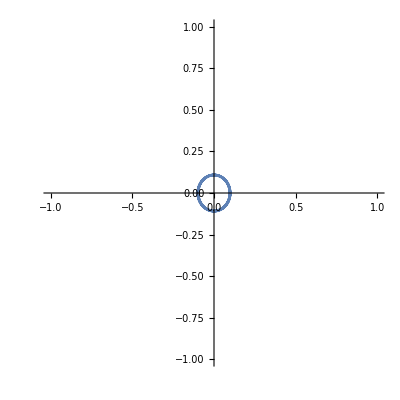
2.Calculating the LCE (Lyapunov characteristic exponent): 
The calculation method we use is to calculate the LCE in every time-step and average over it, where the calculation time-step we set is 1. You can see that as time goes up, the average of LCE converge to a certain value. 

Now we calculate the LCE (Lyapunov characteristic exponent) in a non-chaotic regime. We set the Parameter and initial conditions in this way: θ0 =0.1;ωθ0 =0;ϕ0=0;ωϕ0=0; α = 0.1, β = 0.1, rm = 9 , rl = 0.2. You can see from the phase plot(θ,ωθ) that this is a non-chaotic regime. In this non-chaotic system, we can get a negative Lyapunov exponent. 
-Graphics-

```mathematica
θ0 =10^-20;ωθ0 =0;ϕ0=0;ωϕ0=0;
d0=10^-20;
θ10 = 10^-20+d0;ωθ10=0;ϕ10=0;ωϕ10=0;
tin=0;tfin=200;
tstep=10;
acc=10;
lcedata={};
sum=0;
```

For t = 10 ,  LCE = -0.0050242

For t = 20 ,  LCE = 0.0125497

For t = 30 ,  LCE = 0.0136746

For t = 40 ,  LCE = 0.0110541

For t = 50 ,  LCE = 0.00888026

For t = 60 ,  LCE = -0.00325997

For t = 70 ,  LCE = -0.00427381

For t = 80 ,  LCE = -0.0138005

For t = 90 ,  LCE = -0.0096233

For t = 100 ,  LCE = -0.0105823

For t = 110 ,  LCE = -0.0104514

For t = 120 ,  LCE = -0.0132562

For t = 130 ,  LCE = -0.0150487

For t = 140 ,  LCE = -0.0124135

For t = 150 ,  LCE = -0.0112547

For t = 160 ,  LCE = -0.0120311

For t = 170 ,  LCE = -0.0118609

For t = 180 ,  LCE = -0.0114708

For t = 190 ,  LCE = -0.0126232

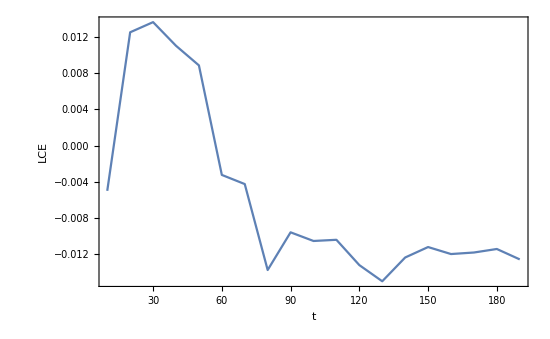

```mathematica
For[i=1,i<tfin/tstep,i++,
doublependulum=
{θ''[τ]+0.001 ϕ''[τ]Cos[θ[τ]-ϕ[τ]]+0.001 ϕ'[τ]^2 Sin[θ[τ]-ϕ[τ]]+1.2Sin[θ[τ]]==0,
ϕ''[τ]+0.001  θ''[τ]Cos[θ[τ]-ϕ[τ]]+0.001  θ'[τ]^2 Sin[θ[τ]-ϕ[τ]]+0.6Sin[ϕ[τ]]==0,
θ1''[τ]+0.001 ϕ1''[τ]Cos[θ1[τ]-ϕ1[τ]]+0.001 ϕ1'[τ]^2 Sin[θ1[τ]-ϕ1[τ]]+1.2 Sin[θ1[τ]]==0,
ϕ1''[τ]+0.001 θ1''[τ]Cos[θ1[τ]-ϕ1[τ]]+0.001  θ1'[τ]^2 Sin[θ1[τ]-ϕ1[τ]]+0.6 Sin[ϕ1[τ]]==0,
θ[0]== θ0,θ'[0]== ωθ0,ϕ[0]== ϕ0,ϕ'[0]== ωϕ0,
θ1[0]== θ10,θ1'[0]== ωθ10,ϕ1[0]== ϕ10,ϕ1'[0]== ωϕ10};
sol=NDSolve[doublependulum,{θ[τ],ϕ[τ],θ1[τ],ϕ1[τ]},{τ,0,tstep},MaxSteps->Infinity,Method->"Adams",PrecisionGoal->acc,AccuracyGoal->acc];
θθ[τ_]=θ[τ]/.sol[[1]];
ϕϕ[τ_]=ϕ[τ]/.sol[[1]];
θθ1[τ_]=θ1[τ]/.sol[[1]];
ϕϕ1[τ_]=ϕ1[τ]/.sol[[1]];


d1=Sqrt[(θθ[tstep]-θθ1[tstep])^2+(ϕϕ[tstep]-ϕϕ1[tstep])^2+(θθ'[tstep]-θθ1'[tstep])^2+(ϕϕ'[tstep]-ϕϕ1'[tstep])^2];

sum+=Log[d1/d0];
lce=sum/(tstep*i);
AppendTo[lcedata,{tstep*i,lce}];
n1=(θθ[tstep]-θθ1[tstep])*(d0/d1);
n2=(ϕϕ[tstep]-ϕϕ1[tstep])*(d0/d1);
n3=(θθ'[tstep]-θθ1[tstep])*(d0/d1);
n4=(ϕϕ'[tstep]-ϕϕ1'[tstep])*(d0/d1);

θ0=θθ[tstep];
ωθ0=θθ'[tstep];
ϕ0= ϕϕ[tstep];
ωϕ0=ϕϕ'[tstep];

θ10=θ0+n1;
ωθ10=ωθ0+n2;
ϕ10= ϕ0+n3;
ωϕ10=ωϕ0+n4;

If[Mod[tstep*i,10]==0,Print[" For t = ",tstep*i," , "," LCE = ",lce]]]

S0=ListPlot[{lcedata},Frame->True,Axes->False,PlotRange->All,Joined->True,FrameLabel->{"t","LCE"},FrameStyle->Directive["Helvetica",17],ImageSize->550]
```

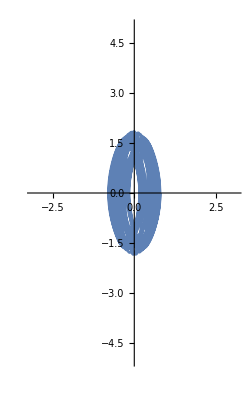
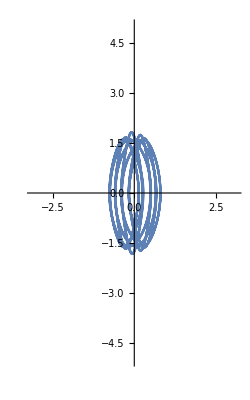
Now we calculate the LCE (Lyapunov characteristic exponent) in a chaotic regime. We set the Parameter and initial conditions in this way: θ0 =0.8;ωθ0 =0;ϕ0=0;ωϕ0=0;α=1.2;β=0.75;rm=0.5 ;rl=0.5;
You can see from the phase plots(θ,ωθ) that this is a chaotic regime. The two phase plots’ initial condition are θ0 =0.8;ωθ0 =0;ϕ0=0;ωϕ0=0 and θ0 =0.8;ωθ0 =0;ϕ0=0.01;ωϕ0=0, respectively. It is very clear that the motion of these two are quite different due to the tiny change in initial conditions.
In this chaotic system, we can get a positive Lyapunov exponent. 
-Graphics--Graphics-

```mathematica
θ0 =0.8;ωθ0 =0;ϕ0=0;ωϕ0=0;
d0=10^-2;
θ10 = 0.8;ωθ10=0;ϕ10=0+d0;ωϕ10=0;
tin=0;tfin=150;
tstep=1;
acc=10;

lcedata={};
sum=0;
```

For t = 5 ,  LCE = 2.60581

For t = 10 ,  LCE = 2.69084

For t = 15 ,  LCE = 2.97469

For t = 20 ,  LCE = 2.81781

For t = 25 ,  LCE = 2.80836

For t = 30 ,  LCE = 2.82618

For t = 35 ,  LCE = 2.82344

For t = 40 ,  LCE = 2.75561

For t = 45 ,  LCE = 2.73703

For t = 50 ,  LCE = 2.76256

For t = 55 ,  LCE = 2.82011

For t = 60 ,  LCE = 2.80832

For t = 65 ,  LCE = 2.78082

For t = 70 ,  LCE = 2.80455

For t = 75 ,  LCE = 2.82471

For t = 80 ,  LCE = 2.79582

For t = 85 ,  LCE = 2.80268

For t = 90 ,  LCE = 2.82582

For t = 95 ,  LCE = 2.82256

For t = 100 ,  LCE = 2.7856

For t = 105 ,  LCE = 2.80153

For t = 110 ,  LCE = 2.81314

For t = 115 ,  LCE = 2.79217

For t = 120 ,  LCE = 2.79448

For t = 125 ,  LCE = 2.799

For t = 130 ,  LCE = 2.82461

For t = 135 ,  LCE = 2.81189

For t = 140 ,  LCE = 2.79105

For t = 145 ,  LCE = 2.81462

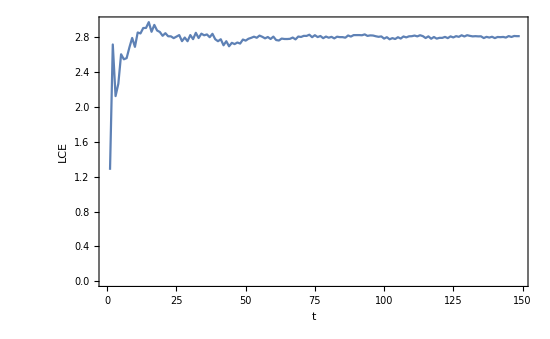

```mathematica
For[i=1,i<tfin/tstep,i++,
doublependulum=
{θ''[τ]+1.2 ϕ''[τ]Cos[θ[τ]-ϕ[τ]]+1.2 ϕ'[τ]^2 Sin[θ[τ]-ϕ[τ]]+2.7Sin[θ[τ]]==0,
ϕ''[τ]+0.75 θ''[τ]Cos[θ[τ]-ϕ[τ]]+0.75  θ'[τ]^2 Sin[θ[τ]-ϕ[τ]]+2.25Sin[ϕ[τ]]==0,
θ1''[τ]+1.2 ϕ1''[τ]Cos[θ1[τ]-ϕ1[τ]]+1.2 ϕ1'[τ]^2 Sin[θ1[τ]-ϕ1[τ]]+2.7 Sin[θ1[τ]]==0,
ϕ1''[τ]+0.75 θ1''[τ]Cos[θ1[τ]-ϕ1[τ]]+0.75  θ1'[τ]^2 Sin[θ1[τ]-ϕ1[τ]]+2.25 Sin[ϕ1[τ]]==0,θ[0]== θ0,θ'[0]== ωθ0,ϕ[0]== ϕ0,ϕ'[0]== ωϕ0,
θ1[0]== θ10,θ1'[0]== ωθ10,ϕ1[0]== ϕ10,ϕ1'[0]== ωϕ10};
sol=NDSolve[doublependulum,{θ[τ],ϕ[τ],θ1[τ],ϕ1[τ]},{τ,0,tstep},MaxSteps->Infinity,Method->"Adams",PrecisionGoal->acc,AccuracyGoal->acc];
θθ[τ_]=θ[τ]/.sol[[1]];
ϕϕ[τ_]=ϕ[τ]/.sol[[1]];
θθ1[τ_]=θ1[τ]/.sol[[1]];
ϕϕ1[τ_]=ϕ1[τ]/.sol[[1]];


d1=Sqrt[(θθ[tstep]-θθ1[tstep])^2+(ϕϕ[tstep]-ϕϕ1[tstep])^2+(θθ'[tstep]-θθ1'[tstep])^2+(ϕϕ'[tstep]-ϕϕ1'[tstep])^2];

sum+=Log[d1/d0];
lce=sum/(tstep*i);
AppendTo[lcedata,{tstep*i,lce}];
n1=(θθ[tstep]-θθ1[tstep])*(d0/d1);
n2=(ϕϕ[tstep]-ϕϕ1[tstep])*(d0/d1);
n3=(θθ'[tstep]-θθ1[tstep])*(d0/d1);
n4=(ϕϕ'[tstep]-ϕϕ1'[tstep])*(d0/d1);

θ0=θθ[tstep];
ωθ0=θθ'[tstep];
ϕ0= ϕϕ[tstep];
ωϕ0=ϕϕ'[tstep];

θ10=θ0+n1;
ωθ10=ωθ0+n2;
ϕ10= ϕ0+n3;
ωϕ10=ωϕ0+n4;

i=i++;
If[Mod[tstep*i,5]==0,Print[" For t = ",tstep*i," , "," LCE = ",lce]]]


S0=ListPlot[{lcedata},Frame->True,Axes->False,PlotRange->All,Joined->True,FrameLabel->{"t","LCE"},FrameStyle->Directive["Helvetica",17],ImageSize->550]
```